```mathematica
Example={{0,1,1,0,0},{1,0,1,0,0},{1,1,0,1,0},{0,0,1,0,1},{0,0,0,1,0}};
```

```mathematica
Example//MatrixForm
```

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

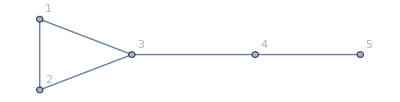

```mathematica
AdjacencyGraph[Example,VertexLabels->Automatic]
```

```mathematica
Eigensystem[Example]//N
```

{{2.21432,-1.67513,-1.,1.,-0.539189},{{3.21432,3.21432,3.90321,2.21432,1.},{-0.675131,-0.675131,1.80606,-1.67513,1.},{-1.,1.,0.,0.,0.},{-1.,-1.,0.,2.,2.},{0.460811,0.460811,-0.709275,-0.539189,1.}}}

```mathematica
1/2.2143197433775352//N
```

0.451606

```mathematica
Eigenvalues[MatrixExp[IdentityMatrix[5]-0.3 Example]]
```

{4.49308,3.6693,3.19554,2.01375,1.39892}

```mathematica
Eigenvalues[MatrixLog[IdentityMatrix[5]-0.3 Example]]
```

{-1.09153,0.407157,-0.356675,0.262364,0.149933}

```mathematica
Eigenvalues[MatrixExp[1/(√2)MatrixLog[IdentityMatrix[5]-0.3 Example]]]
```

{1.33363,1.20384,1.11184,0.777084,0.462169}

```mathematica
(* comparison with the theory *)
```

```mathematica
Eigenvalues[IdentityMatrix[5]-0.3 Example]
```

{1.50254,1.3,1.16176,0.7,0.335704}

```mathematica
Exp[Eigenvalues[IdentityMatrix[5]-0.3 Example]]
```

{4.49308,3.6693,3.19554,2.01375,1.39892}

```mathematica
Log[Eigenvalues[IdentityMatrix[5]-0.3 Example]]
```

{0.407157,0.262364,0.149933,-0.356675,-1.09153}

```mathematica
Exp[1/(√2)Log[Eigenvalues[IdentityMatrix[5]-0.3 Example]]]
```

{1.33363,1.20384,1.11184,0.777084,0.462169}